## Frequently Used Hamiltonians

```mathematica
(* a: M.Cho, H.M.Vaswani, T.Brixner, J.Stenger, and G.R.Fleming, J.Phys.Chem.B 109,10542 (2005)*)
hFMO7a=({{280., -106., 8., -5., 6., -8., -4.}, {-106., 420., 28., 6., 2., 13., 1.}, {8., 28., 0., -62., -1., -9., 17.}, {-5., 6., -62., 175., -70., -19., -57.}, {6., 2., -1., -70., 320., 40., -2.}, {-8., 13., -9., -19., 40., 360., 32.}, {-4., 1., 17., -57., -2., 32., 260.}});
hFMO7a12=({{280., -106.}, {-106., 420.}});
hFMO7a56=({{320., 40.}, {40., 360.}});
hFMO7a47=({{175., -57.}, {-57., 260.}});
s12=
ArrayPad[Eigenvectors[hFMO7a12],{0,5}]+IdentityMatrix[7]-SparseArray[{{1,1}->1,{2,2}->1},7];

s12t=
ArrayPad[Eigenvectors[hFMO7a12]ᵀ,{0,5}]+IdentityMatrix[7]-SparseArray[{{1,1}->1,{2,2}->1},7];

s56=
ArrayPad[Eigenvectors[hFMO7a56],{4,1}]+IdentityMatrix[7]-SparseArray[{{5,5}->1,{6,6}->1},7];

s56t=
ArrayPad[Eigenvectors[hFMO7a56]ᵀ,{4,1}]+IdentityMatrix[7]-SparseArray[{{5,5}->1,{6,6}->1},7];

s47=
SparseArray[{{4,4}->Eigenvectors[hFMO7a47]⟦1,1⟧,{7,7}->Eigenvectors[hFMO7a47]⟦2,2⟧,{4,7}->Eigenvectors[hFMO7a47]⟦1,2⟧,{7,4}->Eigenvectors[hFMO7a47]⟦2,1⟧},7]+IdentityMatrix[7]-SparseArray[{{4,4}->1,{7,7}->1},7];
s47t=
SparseArray[{{4,4}->Eigenvectors[hFMO7a47]ᵀ⟦1,1⟧,{7,7}->Eigenvectors[hFMO7a47]ᵀ⟦2,2⟧,{4,7}->Eigenvectors[hFMO7a47]ᵀ⟦1,2⟧,{7,4}->Eigenvectors[hFMO7a47]ᵀ⟦2,1⟧},7]+IdentityMatrix[7]-SparseArray[{{4,4}->1,{7,7}->1},7];

(* block diagonalization of hFMO7a *)
(* 
	Usual pathways:
	(1,2)->(4,7)->3
	(5,6)->(4,7)->3
*)
hcFMO7a=Chop[s47.s56.s12.hFMO7a.s47t.s56t.s12t];
hcFMO7a//MatrixForm
```

(477.028 | 0 | 20.8677 | -0.951068 | 12.3942 | 8.93131 | -8.08487
0 | 222.972 | -20.311 | 2.02515 | -2.5224 | 5.76654 | -2.76208
20.8677 | -20.311 | 0 | 42.9998 | -8.18159 | -3.88093 | 47.7914
-0.951068 | 2.02515 | 42.9998 | 288.6 | 47.1427 | -5.66741 | 0
12.3942 | -2.5224 | -8.18159 | 47.1427 | 384.721 | 0 | 35.6025
8.93131 | 5.76654 | -3.88093 | -5.66741 | 0 | 295.279 | -52.6014
-8.08487 | -2.76208 | 47.7914 | 0 | 35.6025 | -52.6014 | 146.4)

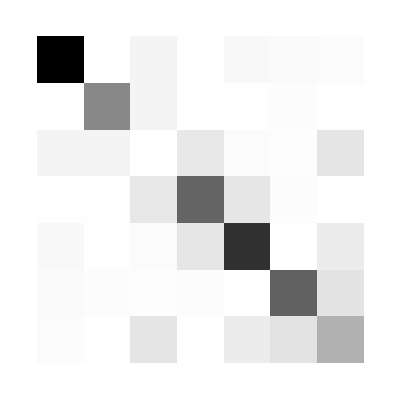

```mathematica
ArrayPlot[hcFMO7a]
```

```mathematica
(* a: G.S.Schlau-Cohen et al., J.Phys.Chem.B 2009,113,15352–15363 *)
hLHCII14a=({{15784, 47.1, -6.1, -2.7, 0.5, -2., -2.6, 3.3, 4.4, -4.5, 24.5, 2.3, -8.4, 2.9}, {47.1, 15103, 17.4, 5.5, -0.2, 4.9, 6.2, -5.8, -21.9, -5.4, 0.7, 10.1, -1.9, 0.1}, {-6.1, 17.4, 15282, -0.5, -0.2, -2.1, 8.2, 4.2, 71.6, 8.4, -0.7, -0.6, 2.4, -5.7}, {-2.7, 5.5, -0.5, 15390, 5.4, 80.8, 26.0, -5.7, -1.5, -0.2, -3.3, 3.7, 2.2, -2.8}, {0.5, -0.2, -0.2, 5.4, 15544, 11.5, -5.2, -3.7, -0.1, 0.8, 1.1, -2.2, -1.2, 0.0}, {-2.0, 4.9, -2.1, 80.8, 11.5, 15888, 23.7, -6.7, -11.8, -0.6, -2.0, 2.1, 1.2, -1.8}, {-2.6, 6.2, 8.2, 26.0, -5.2, 23.7, 15557, -3.5, -1.7, -0.4, -2.1, 2.2, 2.7, -2.4}, {3.3, -5.8, 4.2, -5.7, -3.7, -6.7, -3.5, 15878, 26.1, 57.0, 4.8, -1.3, -2.2, 1.4}, {4.4, -21.9, 71.6, -1.5, -0.1, -11.8, -1.7, 26.1, 15818, 1.1, 3.3, -0.2, -2.5, 2.0}, {-4.5, -5.4, 8.4, -0.2, 0.8, -0.6, -0.4, 57.0, 1.1, 15038, -26.4, 12.4, 6., -1.2}, {24.5, 0.7, -0.7, -3.3, 1.1, -2.0, -2.1, 4.8, 3.3, -26.4, 15180, 105.0, -0.8, 0.6}, {2.3, 10.1, -0.6, 3.7, -2.2, 2.1, 2.2, -1.3, -0.2, 12.4, 105.0, 15082, -1.0, -0.2}, {-8.4, -1.9, 2.4, 2.2, -1.2, 1.2, 2.7, -2.2, -2.5, 6.0, -0.8, -1.0, 15180, -28.0}, {2.9, 0.1, -5.7, -2.8, 0.0, -1.8, -2.4, 1.4, 2.0, -1.2, 0.6, -0.2, -28.0, 15309}});
```